Integrand Investigations

```mathematica
Get["TransportFunctions/Integrands.m"];
```

### testing precision of aperture function in integrand

```mathematica
ListPlot3D[Flatten[Table[{p/1000.,x0,IntegrandApert[0.,{-0.05,p,Pi/4,Pi,0.2,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,2}]},{x0,-0.01,0.01,0.02/50},{p,500000,700000,200000/30}],1]]//AbsoluteTiming
```

{69.8594,-Graphics3D-}

```mathematica
ListPlot3D[Flatten[Table[{p/1000.,x0,IntegrandApert[0.,{-0.05,p,Pi/4,Pi,0.2,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}]},{x0,-0.01,0.01,0.02/50},{p,500000,700000,200000/30}],1]]//AbsoluteTiming
```

{74.5943,-Graphics3D-}

```mathematica
ListPlot3D[Flatten[Table[{p/1000.,x0,IntegrandApert[0.,{-0.05,p,Pi/4,Pi,0.2,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,4}]},{x0,-0.01,0.01,0.02/50},{p,500000,700000,200000/30}],1]]//AbsoluteTiming
```

{76.5922,-Graphics3D-}

```mathematica
Get["TransportFunctions/IntegrationTest.m"];
```

```mathematica
Plot3D[IntegrandApert[0.,{-0.05,p,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{p,0,pmax},{x0,-0.02,0.02},PlotRange->All,PlotPoints->40]
```

-Graphics3D-

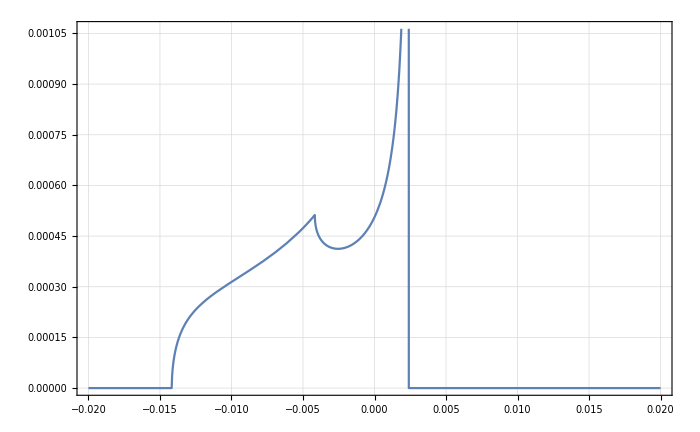

```mathematica
Plot[IntegrandApert[0.,{-0.05,700000,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{x0,-0.02,0.02}]
```

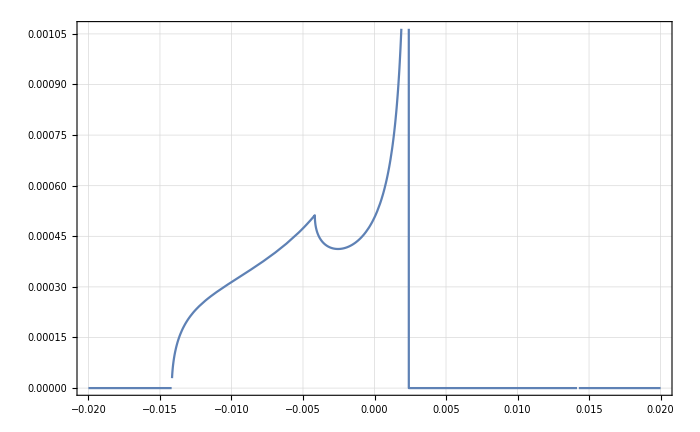

```mathematica
Plot[IntegrandApertPiecewise[0.,{-0.05,700000,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{x0,-0.02,0.02}]
```

```mathematica
Plot[IntegrandApertBoole[0.,{-0.05,700000,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{x0,-0.02,0.02}]
```

-Graphics-

### lets see how this 1D sub integrand is integrated for different types of boolean x0-limitations

```mathematica
NIntegrate[IntegrandApert[0.,{-0.05,700000,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{x0,-0.02,0.02},PrecisionGoal->4,Method->{"GlobalAdaptive","SymbolicProcessing"->False},MaxRecursion->30]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{28.0845,7.53057×10^-6}

```mathematica
NIntegrate[IntegrandApert[0.,{-0.05,700000,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{x0,-0.02,0.02},PrecisionGoal->4,Method->{"GlobalAdaptive"},MaxRecursion->30]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{28.8584,7.53057×10^-6}

```mathematica
NIntegrate[IntegrandApertN[0.,{-0.05,700000,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{x0,-0.02,0.02},PrecisionGoal->4,Method->{"GlobalAdaptive","SymbolicProcessing"->False},MaxRecursion->30]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{28.9197,7.53057×10^-6}

```mathematica
NIntegrate[IntegrandApertPiecewise[0.,{-0.05,700000,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{x0,-0.02,0.02},PrecisionGoal->4,Method->{"GlobalAdaptive","SymbolicProcessing"->False},MaxRecursion->30]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{28.6516,7.53057×10^-6}

```mathematica
NIntegrate[IntegrandApertBoole[0.,{-0.05,700000,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{x0,-0.02,0.02},PrecisionGoal->4,Method->{"GlobalAdaptive","SymbolicProcessing"->False},MaxRecursion->30]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{28.8162,7.53057×10^-6}

### check the other coordinates of integration

```mathematica
?pminCases
```

```mathematica
NIntegrate[IntegrandApert[0.,{-0.05,p,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{p,-0.02,0.02},PrecisionGoal->4,Method->{"GlobalAdaptive","SymbolicProcessing"->False},MaxRecursion->30]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{28.0845,7.53057×10^-6}

```mathematica
NIntegrate[IntegrandApert[0.,{-0.05,700000,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{x0,-0.02,0.02},PrecisionGoal->4,Method->{"GlobalAdaptive"},MaxRecursion->30]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{28.8584,7.53057×10^-6}

```mathematica
NIntegrate[IntegrandApertN[0.,{-0.05,700000,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{x0,-0.02,0.02},PrecisionGoal->4,Method->{"GlobalAdaptive","SymbolicProcessing"->False},MaxRecursion->30]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{28.9197,7.53057×10^-6}

```mathematica
NIntegrate[IntegrandApertPiecewise[0.,{-0.05,700000,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{x0,-0.02,0.02},PrecisionGoal->4,Method->{"GlobalAdaptive","SymbolicProcessing"->False},MaxRecursion->30]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{28.6516,7.53057×10^-6}

```mathematica
NIntegrate[IntegrandApertBoole[0.,{-0.05,700000,Pi/4,Pi,0.18,1.,1.},{0.01,0.035,0.,0.,x0,0.,1.,3}],{x0,-0.02,0.02},PrecisionGoal->4,Method->{"GlobalAdaptive","SymbolicProcessing"->False},MaxRecursion->30]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{28.8162,7.53057×10^-6}

### symbolic processing doesnt cost a lot of time. other integrands take a little longer.now see for multi dim integral

```mathematica
GlobalAdaptiveRules={"GaussBerntsenEspelidRule","GaussKronrodRule","LobattoKronrodRule","ClenshawCurtisRule","CartesianRule","MultidimensionalRule"};
```

```mathematica
IntOptionListMaker[Prec_,Accur_]:=Sequence@(Join[{PrecisionGoal->Prec,AccuracyGoal->Accur},{#}])&/@{
Method->{"GlobalAdaptive",Method->"MultidimensionalRule",MaxRecursion->30},
Method->{"GlobalAdaptive",Method->"MultidimensionalRule","SingularityHandler"->None,"SymbolicProcessing"->False,MaxRecursion->30},
Method->{"GlobalAdaptive",Method->"MultidimensionalRule","SingularityHandler"->"DuffyCoordinates","SymbolicProcessing"->False,MaxRecursion->30},
Method->{"QuasiMonteCarlo","MaxPoints"->500000,"SymbolicProcessing"->False},
Method->{"AdaptiveMonteCarlo","MaxPoints"->500000,"SymbolicProcessing"->False},
Method->{"AdaptiveMonteCarlo","MaxPoints"->500000,Method->{"MonteCarloRule","AxisSelector"->{"MinVariance","SubsampleFraction"->1/2}},"SymbolicProcessing"->False}
};
```

```mathematica
CloseKernels[];
LaunchKernels[3];
```

```mathematica
MethodTest=ParallelTable[IntegrationTest[i],{i,IntOptionListMaker[3,3]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::maxp: The integral failed to converge after 459496 integrand evaluations. NIntegrate obtained 1.36583 and 0.00560202 for the integral and error estimates.

{{1.36479,-Graphics3D-,2986.1831,89517},{1.36492,-Graphics3D-,7991.36708,233607},{1.36492,-Graphics3D-,7534.20018,233607},{1.36583,-Graphics3D-,18098.80054,459496},{1.35059,-Graphics3D-,7890.153468,195300},{1.36075,-Graphics3D-,5166.77727,119900}}

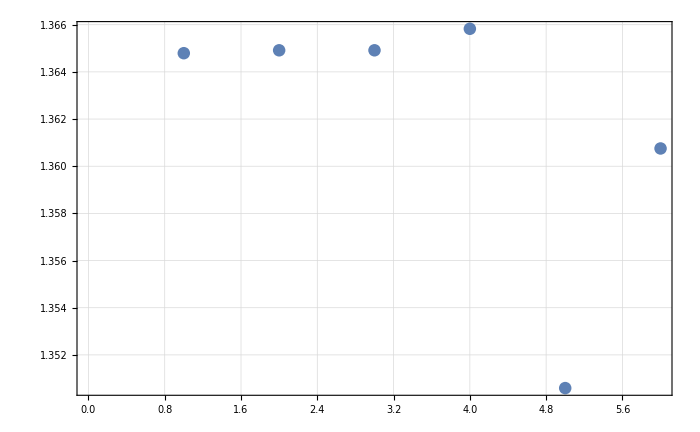

```mathematica
ListPlot[MethodTest[[All,1]]]
```

```mathematica
StandardDeviation[MethodTest[[All,1]]]/Mean[MethodTest[[All,1]]]
```

0.00429545

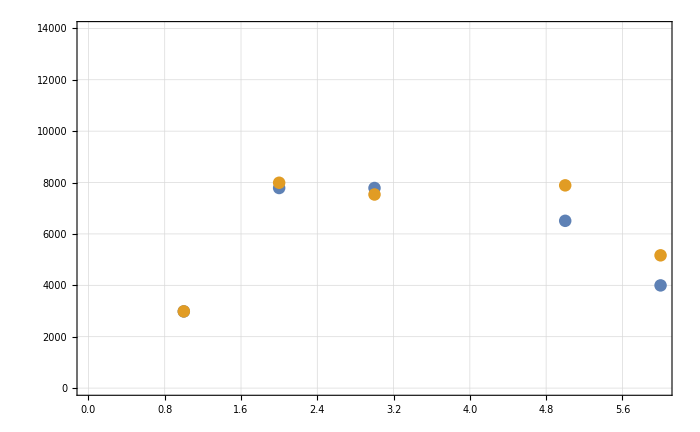

```mathematica
ListPlot[{MethodTest[[All,4]]/30,MethodTest[[All,3]]}]
```

```mathematica
MethodTestBoole=ParallelTable[IntegrationTestBoole[i],{i,IntOptionListMaker[3,3]},Method->"FinestGrained"]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
IntOptionListMaker[3,3][[1]]
```

{PrecisionGoal→3,AccuracyGoal→3,Method→{GlobalAdaptive,Method→MultidimensionalRule,MaxRecursion→30}}

```mathematica
Booletest=IntegrationTestBoole[IntOptionListMaker[3,3][[1]]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{1.3648,-Graphics3D-,11348.96829,89913}